```mathematica
circle3D[centre_: {0,0,0},radius_: 1,normal_: {0,0,1},angle_: {0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle≥2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
Arc3D[{a_,b_,m_},n_: 60,prim_: Line]:=Module[{α,lab,axis,aarc,tm,alpha},lab=m+Norm[a-m]*Normalize[b-m];
axis=(a-m)×(b-m);
aarc=(VectorAngle[a-m,b-m]);
tm=RotationMatrix[alpha,axis];
prim@Table[m+tm.(a-m),{alpha,0,aarc,aarc/n}]]

arrowLength=0.5;
point2 = Normalize@{0,0,1};
point1 = Normalize@{0,0,-1};
mid = (point1+point2)/2;
mid1 = Normalize@Cross[point1, point2];
axis = Normalize@Cross[mid, mid1];
intersect1 = Normalize@{1,0,0};
intersect2= {Cos[θ],-Sin[θ],0};
tinyRad = 0.05;

Chi1 =ArcCos[√(1/2(1+point1[[1]]))];
Phi1=ArcTan[point1[[3]]/point1[[2]]];
points1 = {point2,-Normalize@Cross[point1, intersect1],  {0,0,0}};
points2 = {-Normalize@Cross[point1, intersect1], point1, {0,0,0}};
points3= {point2,-Normalize@Cross[point1, intersect2],  {0,0,0}};
points4 ={-Normalize@Cross[point1, intersect2], point1, {0,0,0}};

azimuths = Table[θ Degree, {θ, 0, 90, 30}];
elevations = Table[θ Degree, {θ, 0, 90, 30}];
points = Table[{Cos[angle1]Cos[angle2], Sin[angle1]Cos[angle2], Sin[angle2]}, {angle2,0, 90Degree, 30Degree}, {angle1,0,90Degree, 90/(4-(Abs@angle2)/(30Degree))Degree}];
points = Flatten[points,1];

chiphi = Table[{ArcCos[√(1/2(1+coord_⟦1⟧))], If[coord_⟦2⟧==0,π/2 Sign[coord_⟦3⟧], ArcTan[coord_⟦3⟧/coord_⟦2⟧]], coord}, {coord, points}];

graphs = Table[{ParametricPlot[{Cos[num_⟦1⟧] Cos[t], Sin[num_⟦1⟧] Cos[t-num_⟦2⟧]}, {t, 0,2 π}, Axes->True, Ticks->False, PlotStyle->{Green,Arrowheads[{0,0,0,0.15,0,0,0,0,0.15,0,0}], Thickness[0.015]}, PlotRange->{{-1.25,1.25},{-1.25,1.25}}]/.Line->Arrow, num_⟦3⟧},{num, chiphi}];

insets = Table[Inset[graph_⟦1⟧, graph_⟦2⟧, {0,0}, 20], {graph, graphs}];
plot1 = ParametricPlot[{Cos[0]Cos[t], Sin[0]Cos[t+π/4]}, {t, -π/2, 2π-π/2},PlotRange->{{-1, 1}, {-1, 1}}, Ticks->False,AxesStyle->Thickness[0.0005
], PlotStyle->{Black,Thickness[0.00075],Arrowheads[{0.07,.07,.07}]}]/.Line->Arrow;

pts=Normalize/@RandomReal[{-1,1},{2,3}];
angles=Table[{0.},Length@pts];
SphericalPlot3D[1,{θ,0,Pi},{ϕ,0,2 Pi},MeshFunctions->Table[With[{v0=v0},Function[{x,y,z,θ,ϕ},VectorAngle[{x,y,z},v0]]],{v0,pts}],Mesh->angles,MeshShading->{{Black,Black},{Black,Automatic}},BoundaryStyle->None]

Graphics3D[{Opacity[0.25],Sphere[{0,0,0},1], 
Opacity[1.0],Arrow[{{0,0,0}, {0,0,1+arrowLength}}], Arrow[{{0,0,0}, {0,1+arrowLength,0}}], Arrow[{{0,0,0}, {1+arrowLength, 0, 0}}], Red,Dashed, circle3D[{0,0,0}, 1, {0,0,1}, {0, 2π}], Thickness[0.005], 
Black,Text[Style["s_1",Bold,24], {1.15+arrowLength,0,0}],
Text[Style["s_2",Bold,24], {0,1.15+arrowLength,0}],
Text[Style["s_3",Bold,24],{0,0,1.15+arrowLength}], 
Dashing[None],Thickness[1]}, 
Boxed->False, ViewPoint->{1,1,0.5}, 
PlotRange->{{-(1+arrowLength), 1+arrowLength}, {-(1+arrowLength), 1+arrowLength}, {-(1), 1+arrowLength}}, 
ImagePadding->None, ViewAngle->Pi/4]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics3D-

-Graphics3D-

```mathematica
graphs = Table[{ParametricPlot[{Cos[num_⟦1⟧] Cos[t], Sin[num_⟦1⟧] Cos[t-num_⟦2⟧]}, {t, 0,2 π}, Axes->False, Ticks->False, PlotStyle->{Black,Arrowheads[{0,0,0,0.25,0,0,0,0,0.25,0,0}], Thickness[0.0005]}, PlotRange->{{-1.25,1.25},{-1.25,1.25}}]/.Line->Arrow, num_⟦3⟧},{num, chiphi}];
outputres = 600;
scale = outputres/72;
insets = Table[Inset[graph_⟦1⟧, graph_⟦2⟧, {0,0}, 40 scale], {graph, graphs}];


exportplot = Graphics3D[{insets, Inset[Graphics[Text[Style["s_1",Black,24 , Bold]]],{1.1+arrowLength,0,0}],Inset[Graphics[Text[Style["s_2",Black,24, Bold]]],{0,1.1+arrowLength,0}],Inset[Graphics[Text[Style["s_3",Black,24, Bold]]],{0,0,1.1+arrowLength}],Thickness[0.005], Opacity[0.25],Sphere[{0,0,0},1], Opacity[1.0],Arrow[{{0,0,0}, {0,0,1+arrowLength}}], Arrow[{{0,0,0}, {0,1+arrowLength,0}}], Arrow[{{0,0,0}, {1+arrowLength, 0, 0}}],Red,Dashed, circle3D[{0,0,0}, 1, {0,0,1}, {0, 2π}]}, Boxed->False, ViewPoint->{1,1,0.5}, PlotRange->{{-(1.15+arrowLength), 1.15+arrowLength}, {-(1.15+arrowLength), 1.15+arrowLength}, {-(1.15), 1.15+arrowLength}}, ImagePadding->None, ViewAngle->Pi/4]


SetDirectory[NotebookDirectory[]]
Export["single_poincare_sphere.tiff", exportplot,ImageResolution->72 scale]
```

-Graphics3D-

/home/lain/Documents/Harvard/metasurface_polarimetry/Graphics

single_poincare_sphere.tiff

```mathematica
exportplot = Graphics3D[{insets, Inset[Graphics[Text[Style["s_1",Black,24, Bold]]],{1.1+arrowLength,0,0}],Inset[Graphics[Text[Style["s_2",Black,24, Bold]]],{0,1.1+arrowLength,0}],Inset[Graphics[Text[Style["s_3",Black,24, Bold]]],{0,0,1.1+arrowLength}],Thickness[0.005], Opacity[0.25],Sphere[{0,0,0},1], Opacity[1.0],Arrow[{{0,0,0}, {0,0,1+arrowLength}}], Arrow[{{0,0,0}, {0,1+arrowLength,0}}], Arrow[{{0,0,0}, {1+arrowLength, 0, 0}}],Red,Dashed, circle3D[{0,0,0}, 1, {0,0,1}, {0, 2π}]}, Boxed->False, ViewPoint->{1,1,0.5}, PlotRange->{{-(1.15+arrowLength), 1.15+arrowLength}, {-(1.15+arrowLength), 1.15+arrowLength}, {-(1.15), 1.15+arrowLength}}, ImagePadding->None, ViewAngle->Pi/4]
```

-Graphics3D-

```mathematica
exportplot
```

-Graphics3D-

Scale[-Graphics3D-,2]

Scale[Scale[-Graphics3D-,2],2]

Scale[B,g]

-Graphics3D-

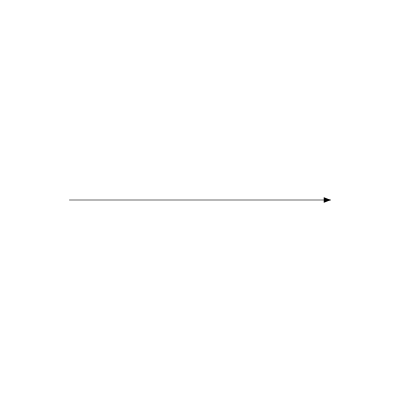

```mathematica
graphs_⟦1,1⟧
```

```mathematica
points = Table[{angle2, angle1}, {angle2, 0, 90, 30}, {angle1,0, 90, 90/(4-angle2/30)}];
```

```mathematica
points
```

{{{0,0},{0,45/2},{0,45},{0,135/2},{0,90}},{{30,0},{30,30},{30,60},{30,90}},{{60,0},{60,45},{60,90}},{{90,0},{90,90}}}

```mathematica
ArcCos[1/(√2)]
```

π/4

```mathematica
coord={0,1,0}
```

{0,1,0}

```mathematica
chiphi = Table[{If[coord_⟦1⟧>0,ArcCos[√(1/2(1+coord_⟦1⟧))], -1/2 ArcCos[coord_⟦1⟧]], If[coord_⟦2⟧==0,π/2 Sign[coord_⟦3⟧], ArcTan[coord_⟦3⟧/coord_⟦2⟧]], coord}, {coord, points}];
```

```mathematica
{ArcCos[√(1/2(1+coord_⟦1⟧))], If[coord_⟦2⟧==0,π/2 Sign[coord_⟦3⟧], ArcTan[coord_⟦3⟧/coord_⟦2⟧]]}
```

{π/4,0}